Go to the line “G=GramMaker[myAntiPyramid[4],14,10000]” and change the 4 to anything you want, then run the note book.

```mathematica
P[n_]:=ArrayFlatten[{{{{0,-1/2},{-1/2,0}},0},{0,IdentityMatrix[n-2]}}]
```

```mathematica
object[v_,f_]:=Polygon/@Map[v[[#1]]&,f,{2}]
face2edges[face_]:=MapThread[Sort[{#1,#2}]&,{face,RotateLeft[face]}]
f2e[f_]:=Union@@face2edges/@f
closest[{P1_,P2_}]:=With[{L=P2-P1},P1-(L.P1 L)/(L.L)]
tangentify[v_,e_]:=Module[{newV=v,t,c},Scan[(
t=closest[v[[#1]]];
c=0.5*(1-Sqrt[t.t])*t;
newV[[#1[[1]]]]+=c;
newV[[#1[[2]]]]+=c;
)&,e];newV]

recenter[v_,e_]:=With[{centroid=Plus@@closest/@Map[v[[#1]]&,e,{2}]/Length[e]},(#1-centroid&)/@v]

unit[x_]:=With[{mag2=x.x},If[mag2≠0,x/Sqrt[mag2],x]]
cross[{ax_,ay_,az_},{bx_,by_,bz_}]:={ay*bz-az*by,az*bx-ax*bz,ax*by-ay*bx}
approxNormal[face_]:=unit[Plus@@MapThread[unit[cross[#1-#2,#2-#3]]&,{face,RotateLeft[face,1],RotateLeft[face,2]}]]
planarize[v_,f_]:=Module[{newV=v,faceXYZ,n,centroid},Scan[(faceXYZ=v[[#1]];n=approxNormal[faceXYZ];
centroid=Plus@@faceXYZ/Length[faceXYZ];
if[n.centroid<0,n=-n];
Scan[newV[[#1]]+=0.2*n.(centroid-v[[#1]])*n&,#1];)&,f];
newV]
canonicalize[v_, f_,prec_,stop_] := 
  Module[{newV = N[v], e = f2e[f], oldV, maxChange}, 
   Do[oldV = newV; newV = tangentify[newV, e]; newV = recenter[newV, e]; 
      newV = planarize[newV, f]; maxChange = Max[Abs[oldV - newV]]; 
      If[maxChange < 10.^(-prec), Break[]], {i, stop}]; 
    newV]
vPyramid[n_]:=N[Join[Table[{Cos[(2*Pi*i)/n],Sin[(2*Pi*i)/n],-2},{i,n}],{{0,0,2}}]]
fPyramid[n_]:=Join[{Range[n]},Table[{i,i+1,n+1},{i,n-1}],{{n,1,n+1}}]
myPyramid[n_]:={vPyramid[n],fPyramid[n]}

vBiPyramid[n_]:=N[Join[Table[{Cos[(2*Pi*i)/n],Sin[(2*Pi*i)/n],0},{i,n}],{{0,0,2}},{{0,0,-2}}]]
fBiPyramid[n_]:=Join[{Range[n]},Table[{i,i+1,n+1},{i,n-1}],{{n,1,n+1}},Table[{i,i+1,n+2},{i,n-1}],{{n,1,n+2}}]
myBiPyramid[n_]:={vBiPyramid[n],fBiPyramid[n]}

vAntiPyramid[n_]:=N[Join[Table[{Cos[2*Pi*(i+0.5)/n],Sin[2*Pi*(i+0.5)/n],-0.5},{i,n}],Table[{Cos[2*Pi*i/n],Sin[2*Pi*i/n],0.5},{i,n}],{{0,0,-1},{0,0,1}}]]
fAntiPyramid[n_]:=Join[{{2n+1,n,n+1,1},{2n+2,2n,n,n+1}},Table[{2n+1,i,n+i+1,i+1},{i,n-1}],Table[{2n+2,n+i,i,n+i+1},{i,n-1}]]
myAntiPyramid[n_]:={vAntiPyramid[n],fAntiPyramid[n]}

vKPrism[k_][n_]:=N[Flatten[Table[Table[{Cos[(2*Pi*i)/n],Sin[(2*Pi*i)/n],-1+2*j/k},{i,n}],{j,0,k}],1]]
fKPrism[k_][n_]:=Join[Table[Range[n]+i*n,{i,0,k}],Table[{i*n,(i-1)*n+1,i*n+1,(i+1)*n},{i,k}],Flatten[Table[Table[{(j-1)*n+i,(j-1)*n+i+1,j*n+i+1,j*n+i},{i,n-1}],{j,k}],1]]
myKPrism[k_][n_]:={vKPrism[k][n],fKPrism[k][n]}

vAntiPrism[n_]:=N[Join[Table[{Cos[2*Pi*i/n],Sin[2*Pi*i/n],-1},{i,n}],Table[{Cos[2*Pi*(i+0.5)/n],Sin[2*Pi*(i+0.5)/n],1},{i,n}]]]
fAntiPrism[n_]:=Join[{Range[n],Range[n]+n,{n,1,2*n},{2*n,1,n+1}},Table[{i,i+1,n+i},{i,n-1}],Table[{n+i-1,i,n+i},{i,2,n}]]
myAntiPrism[n_]:={vAntiPrism[n],fAntiPrism[n]}

vHermaphrodite[n_]:=N[Join[Table[{Cos[(2*Pi*i)/n],Sin[(2*Pi*i)/n],-1},{i,n}],Table[{Cos[(2*Pi*i)/n],Sin[(2*Pi*i)/n],0},{i,n}],{{0,0,1}}]]
fHermaphrodite[n_]:=Join[{Range[n],{1,n+1,2*n,n},{n+1,2*n,2*n+1}},Table[{i,i+1,n+i+1,n+i},{i,n-1}],Table[{n+i,n+i+1,2*n+1},{i,n-1}]]
myHermaphrodite[n_]:={vHermaphrodite[n],fHermaphrodite[n]}

vAntiHermaphrodite[n_]:=N[Join[Table[{Cos[2*Pi*i/n],Sin[2*Pi*i/n],-1},{i,n}],Table[{Cos[2*Pi*(i+0.5)/n],Sin[2*Pi*(i+0.5)/n],0},{i,n}],{{0,0,1}}]]
fAntiHermaphrodite[n_]:=Join[{Range[n],{1,2*n,n},{1,n+1,2*n+1,2*n}},Table[{i,i+1,n+i},{i,n-1}],Table[{i,n+i,2*n+1,n+i-1},{i,2,n}]]
myAntiHermaphrodite[n_]:={vAntiHermaphrodite[n],fAntiHermaphrodite[n]}
vNew[myShape_,prec_,stop_]:=canonicalize[myShape[[1]],myShape[[2]],prec,stop]
spherebbhhhCoords[point_]:={1/√(point.point-1),1/√(point.point-1),point[[1]]/√(point.point-1),point[[2]]/√(point.point-1),point[[3]]/√(point.point-1)}
cMatrix[myShape_,prec_,stop_]:=Transpose[Map[spherebbhhhCoords,vNew[myShape,prec,stop]]]
GramMaker[myShape_,prec_,stop_]:= With[{cFin =cMatrix[myShape,prec,stop]}, Transpose[cFin].{{0,-1/2,0,0,0},{-1/2,0,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}.cFin]
```

```mathematica
G=GramMaker[myAntiPyramid[5],14,10000]
```

{{1.,-4.23607,-12.7082,-12.7082,-4.23607,-1.,-1.,-9.47214,-14.7082,-9.47214,-1.,-2.23607},{-4.23607,1.,-4.23607,-12.7082,-12.7082,-9.47214,-1.,-1.,-9.47214,-14.7082,-1.,-2.23607},{-12.7082,-4.23607,1.,-4.23607,-12.7082,-14.7082,-9.47214,-1.,-1.,-9.47214,-1.,-2.23607},{-12.7082,-12.7082,-4.23607,1.,-4.23607,-9.47214,-14.7082,-9.47214,-1.,-1.,-1.,-2.23607},{-4.23607,-12.7082,-12.7082,-4.23607,1.,-1.,-9.47214,-14.7082,-9.47214,-1.,-1.,-2.23607},{-1.,-9.47214,-14.7082,-9.47214,-1.,1.,-4.23607,-12.7082,-12.7082,-4.23607,-2.23607,-1.},{-1.,-1.,-9.47214,-14.7082,-9.47214,-4.23607,1.,-4.23607,-12.7082,-12.7082,-2.23607,-1.},{-9.47214,-1.,-1.,-9.47214,-14.7082,-12.7082,-4.23607,1.,-4.23607,-12.7082,-2.23607,-1.},{-14.7082,-9.47214,-1.,-1.,-9.47214,-12.7082,-12.7082,-4.23607,1.,-4.23607,-2.23607,-1.},{-9.47214,-14.7082,-9.47214,-1.,-1.,-4.23607,-12.7082,-12.7082,-4.23607,1.,-2.23607,-1.},{-1.,-1.,-1.,-1.,-1.,-2.23607,-2.23607,-2.23607,-2.23607,-2.23607,1.,-1.76393},{-2.23607,-2.23607,-2.23607,-2.23607,-2.23607,-1.,-1.,-1.,-1.,-1.,-1.76393,1.}}

```mathematica
G={{1,-1,-1,-1,-1},{-1,1,-1,-3,-1},{-1,-1,1,-1,-3},{-1,-3,-1,1,-1},{-1,-1,-3,-1,1}}
```

{{1,-1,-1,-1,-1},{-1,1,-1,-3,-1},{-1,-1,1,-1,-3},{-1,-3,-1,1,-1},{-1,-1,-3,-1,1}}

```mathematica
vertices=Length[G]
```

5

```mathematica
MatrixForm[G]
```

(1 | -1 | -1 | -1 | -1
-1 | 1 | -1 | -3 | -1
-1 | -1 | 1 | -1 | -3
-1 | -3 | -1 | 1 | -1
-1 | -1 | -3 | -1 | 1)

```mathematica
d=4
```

4

```mathematica
Sign[Eigenvalues[P[d]]]
```

{1,1,-1,1}

```mathematica
Sign[Eigenvalues[G]]
```

{-1,1,1,1,0}

```mathematica
MatrixForm[Perm=IdentityMatrix[d][[All,Ordering@{3,2,1,4}]]];
```

```mathematica
V1a=(DiagonalMatrix[Abs[Eigenvalues[P[d]]^0.5]].DiagonalMatrix[Sign[Eigenvalues[P[d]]]]);
V1b=Orthogonalize[Eigenvectors[P[d]]];
V1=Perm.V1a.V1b;
MatrixForm[T1=Perm.DiagonalMatrix[Sign[Eigenvalues[P[d]]]].Perm];
MatrixForm[Transpose[V1].T1.V1];
```

```mathematica
V2a=(DiagonalMatrix[Abs[Eigenvalues[G]^0.5]].DiagonalMatrix[Sign[Eigenvalues[G]]]);
V2b=Orthogonalize[N[Eigenvectors[G],100]];
MatrixForm[V2=V2a.V2b];
T2=DiagonalMatrix[Sign[Eigenvalues[G]]];
MatrixForm[Transpose[V2].T2.V2];
MatrixForm[V2];
MatrixForm[reducer=Table[If[i==j,1,0],{i,d},{j,vertices}]];
MatrixForm[c=Inverse[V1].reducer.V2];
MatrixForm[Transpose[c].P[d].c];
```

(1.94863 | 0.807149 | 0.807149 | 0.807149 | 0.807149
-0.513181 | 1.23893 | 1.23893 | 1.23893 | 1.23893
0. | 0. | -1.41421 | 0. | 1.41421
0. | -1.41421 | 0. | 1.41421 | 0.
0 | 0 | 0 | 0 | 0)

{-0.513181,1.23893,1.23893,1.23893,1.23893}

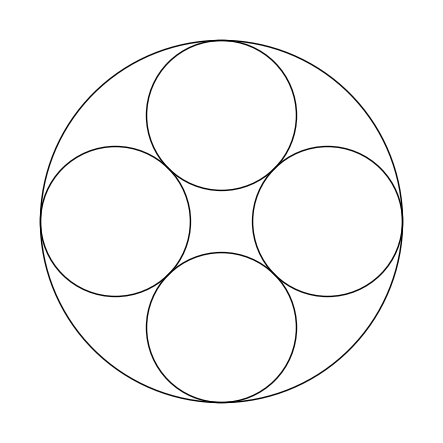

```mathematica
MatrixForm[c=If[Length[c]==4,Join[c,{ConstantArray[0,vertices]}],c]]
c⟦2,All⟧
Graphics[
Table[
If[c[[All,i]][[2]]==0,
InfiniteLine[
{If[c[[All,i]][[3]]==0,
{0,c[[All,i]][[1]]/2},
If[c[[All,i]][[4]]==0,
{c[[All,i]][[1]]/2,0},{0,c[[All,i]][[1]]/(2c[[All,i]][[4]])}]],

If[c[[All,i]][[3]]==0,
{1,c[[All,i]][[1]]/2},
If[c[[All,i]][[4]]==0,
{c[[All,i]][[1]]/2,1},{1,c[[All,i]][[1]]/(2c[[All,i]][[4]])-c[[All,i]][[3]]/c[[All,i]][[4]]}]]}],

Circle[{c[[All,i]][[3]]/c[[All,i]][[2]],c[[All,i]][[4]]/c[[All,i]][[2]]},Abs[1/c[[All,i]][[2]]]]],
{i,vertices}]]
```